### Jz, J+, J- Construction

```mathematica
(*add the cavity photon expectation number to the collective tls expectation number to check if it stays constant or not-should for tc models, probably not for the rest (counter-rotating terms).*)
Jz[K_Integer]:=Module[{J,dim,Jz},
J=K/2;
dim=2 J+1;
Jz=SparseArray[DiagonalMatrix[Reverse[Range[-J,J]]]];
Return[Jz];
]

Jp[K_Integer]:=Module[{J,dim,Jplus,mValues,i,j},
J=K/2;
dim=2 J+1;
Jplus=SparseArray[{},{dim,dim}];
mValues=Reverse[Range[-J,J]];
For[i=1,i<dim,i++,
Jplus[[i,i+1]]=Sqrt[J * (J+1) - mValues[[i+1]] * (mValues[[i+1]]+1)];
];
Return[SparseArray[Jplus]];
]

Jm[K_Integer]:=Module[{J,dim,Jplus,mValues,i,j},
J=K/2;
dim=2 J+1;
Jplus=SparseArray[{},{dim,dim}];
mValues=Reverse[Range[-J,J]];
For[i=2,i<=dim,i++,
Jplus[[i,i-1]]=Sqrt[J * (J+1) - mValues[[i]] * (mValues[[i]]+1)];
];
Return[Jplus];
]
```

### Complete Construction

```mathematica
NUMTLS = 2;
BSIZE = 30;
omegaC =1.000;
omega0 = 1.000;
TCH[j_]:=Module[
{bsize=BSIZE,ω0=omega0,ωc=omegaC,K=NUMTLS,idHO,idTLS,H0HO,HTLS,a,Hindep,Hcoup,Htot},
(*Identity matrix for QHO*)
idHO=SparseArray[IdentityMatrix[bsize]];
idTLS=SparseArray[IdentityMatrix[K+1]];
(*QHO Hamiltonian*)
H0HO=ωc*SparseArray[Band[{1,1}]->Table[n+1/2,{n,0,bsize-1}]];
(*Combined TLS Hamiltonian*)
HTLS=ω0*Jz[K];
(*Annihilation operator definition*)
a=SparseArray[Band[{1,2}]->Table[Sqrt[n],{n,1,bsize-1}],{bsize,bsize}];
(*Independent Hamiltonian*)
Hindep=KroneckerProduct[HTLS,idHO]+KroneckerProduct[idTLS,H0HO];
(*Coupling Hamiltonian*)Hcoup=SetPrecision[j/Sqrt[K] (KroneckerProduct[Jp[K],a]+KroneckerProduct[Jm[K],a†]),50];
(*Total Hamiltonian*)
Htot=Hindep+Hcoup;
Htot]
DH[j_]:=Module[
{bsize=BSIZE,ω0=omega0,ωc=omegaC,K=NUMTLS,idHO,idTLS,H0HO,HTLS,a,Hindep,Hcoup,Htot},
(*Identity matrix for QHO*)
idHO=SparseArray[IdentityMatrix[bsize]];
idTLS=SparseArray[IdentityMatrix[K+1]];
(*QHO Hamiltonian*)
H0HO=ωc*SparseArray[Band[{1,1}]->Table[n+1/2,{n,0,bsize-1}]];
(*Combined TLS Hamiltonian*)
HTLS=ω0*Jz[K];
(*Annihilation operator definition*)
a=SparseArray[Band[{1,2}]->Table[Sqrt[n],{n,1,bsize-1}],{bsize,bsize}];
(*Independent Hamiltonian*)
Hindep=KroneckerProduct[HTLS,idHO]+KroneckerProduct[idTLS,H0HO];
(*Coupling Hamiltonian*)Hcoup=SetPrecision[j/Sqrt[K] (KroneckerProduct[Jp[K],a]+KroneckerProduct[Jm[K],a†]
+ KroneckerProduct[Jp[K],a†]+KroneckerProduct[Jm[K],a]),50];
(*Total Hamiltonian*)
Htot=Hindep+Hcoup;
Htot]
PFH[j_]:=Module[
{bsize=BSIZE,ω0=omega0,ωc=omegaC,K=NUMTLS,idHO,idTLS,H0HO,HTLS,Hdse, a,Hindep,Hcoup,Htot},
(*Identity matrix for QHO*)
idHO=SparseArray[IdentityMatrix[bsize]];
idTLS=SparseArray[IdentityMatrix[K+1]];
(*QHO Hamiltonian*)
H0HO=ωc*SparseArray[Band[{1,1}]->Table[n+1/2,{n,0,bsize-1}]];
(*Combined TLS Hamiltonian*)
HTLS=ω0*Jz[K];
(*Annihilation operator definition*)
a=SparseArray[Band[{1,2}]->Table[Sqrt[n],{n,1,bsize-1}],{bsize,bsize}];
(*Independent Hamiltonian*)
Hindep=KroneckerProduct[HTLS,idHO]+KroneckerProduct[idTLS,H0HO];
(*Coupling Hamiltonian*)Hcoup=SetPrecision[j/Sqrt[K] (KroneckerProduct[Jp[K],a]+KroneckerProduct[Jm[K],a†]
+ KroneckerProduct[Jp[K],a†]+KroneckerProduct[Jm[K],a]),50];
(*DSE Terms*)
Hdse = (j^2)/ωc/K * (KroneckerProduct[(Jp[K] + Jm[K]),idHO]).(KroneckerProduct[(Jp[K] + Jm[K]),idHO]);
(*Total Hamiltonian*)
Htot=Hindep+Hcoup + Hdse;
Htot]
```

### Eigenfunction Plots

#### Solving Eigensystem

```mathematica
coupling=0.07;
{tceigv, tceigs} = Eigensystem[N[TCH[coupling]]];
{deigv, deigs} = Eigensystem[N[DH[coupling]]];
{pfeigv, pfeigs} = Eigensystem[N[PFH[coupling]]];
tcsorted = SortBy[Transpose[{tceigv, tceigs}], First];
dsorted = SortBy[Transpose[{deigv, deigs}], First];
pfsorted = SortBy[Transpose[{pfeigv, pfeigs}], First];

sortedtceigv = tcsorted[[All, 1]];
sortedtceigs = tcsorted[[All, 2]];
sorteddeigv = dsorted[[All, 1]];
sorteddeigs = dsorted[[All, 2]];
sortedpfeigv = pfsorted[[All, 1]];
sortedpfeigs = pfsorted[[All, 2]];
```

#### Checking for Imaginary Components in Eigenstates

```mathematica
(*Define a function to check if a vector has complex elements*)
hasComplexElements[vec_]:=AnyTrue[vec,Im[#]!=0&];

(*Find indices of eigenvectors with complex elements in the Tavis-Cummings model*)
complexIndicesTC=Position[sortedtceigv,_?(hasComplexElements[#]&),{1}];

(*Print out the indices of the eigenvectors with complex elements*)
Print["Indices of Tavis-Cummings eigenvectors with complex elements: ",complexIndicesTC];
```

Indices of Tavis-Cummings eigenvectors with complex elements: {}

#### Plotting

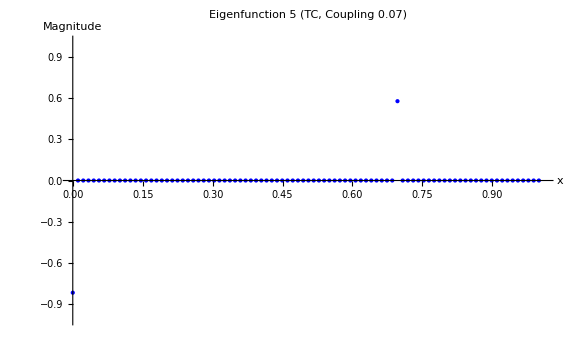

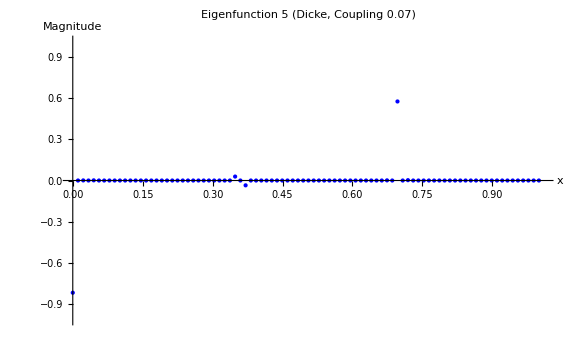

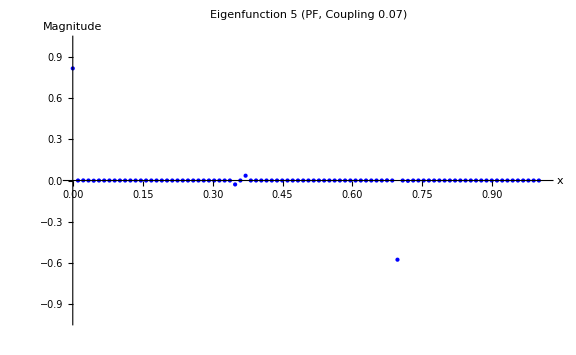

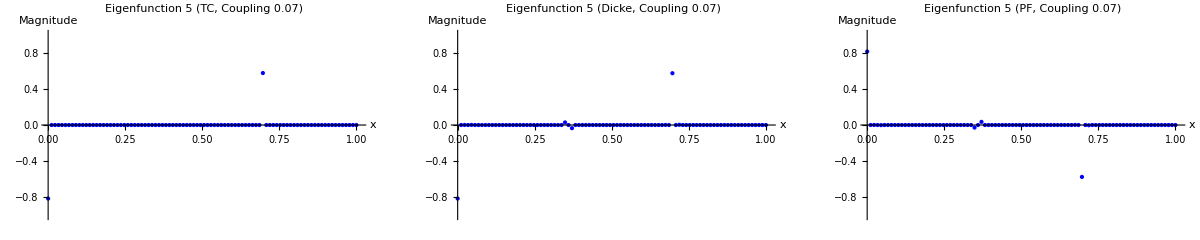

```mathematica
index=5;
(*Extract the specified eigenfunction (corresponding to the index)*)
slice=sortedtceigs[[index]];
data=Transpose[{Subdivide[0,1,Length[slice]-1],slice}];
plottc=ListPlot[data,PlotLabel->"Eigenfunction "<>ToString[index]<>" (TC, Coupling "<>ToString[coupling]<>")",ImageSize->Large,PlotRange->{{0,1.01},{-1.01,1.01}},PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"x","Magnitude"}]

slice=sorteddeigs[[index]];
data=Transpose[{Subdivide[0,1,Length[slice]-1],slice}];
plotd=ListPlot[data,PlotLabel->"Eigenfunction "<>ToString[index]<>" (Dicke, Coupling "<>ToString[coupling]<>")",ImageSize->Large,PlotRange->{{0,1.01},{-1.01,1.01}},PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"x","Magnitude"}]

slice=sortedpfeigs[[index]];
data=Transpose[{Subdivide[0,1,Length[slice]-1],slice}];
plotpf=ListPlot[data,PlotLabel->"Eigenfunction "<>ToString[index]<>" (PF, Coupling "<>ToString[coupling]<>")",ImageSize->Large,PlotRange->{{0,1.01},{-1.01,1.01}},PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"x","Magnitude"}]
GraphicsRow[{plottc,plotd, plotpf}]
```

#### Initial State Projection (Abs Square) Onto Eigenbases

(0
1.
0)

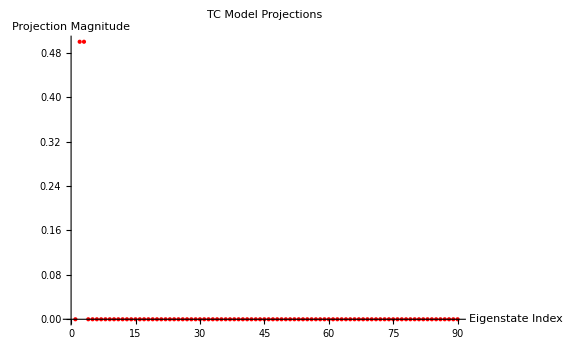

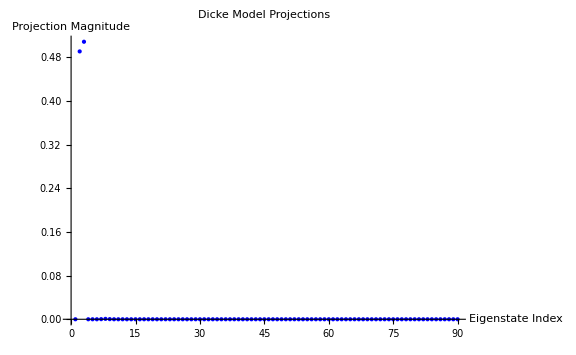

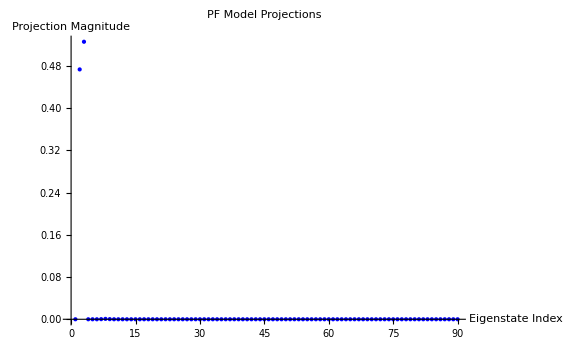

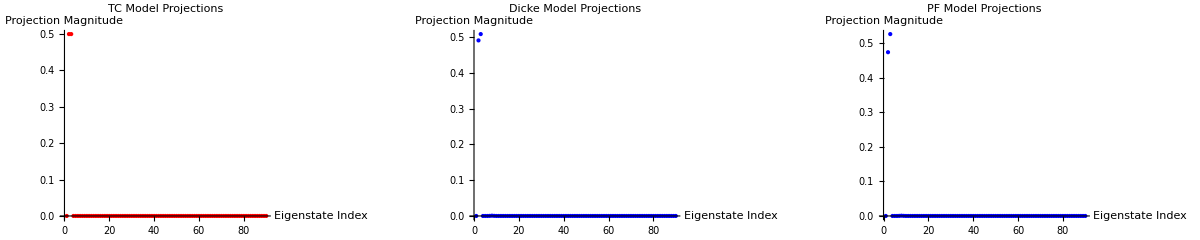

```mathematica
ψ0HO=SparseArray[{1->1.0},BSIZE];
ψ0TLS=SparseArray[{NUMTLS->1.0},NUMTLS+1];
(*ψ0TLS=SparseArray[{1->1.0},NUMTLS+1];*)
(*Define the initial state:vacuum in the cavity and fully excited TLS*)
Print[ψ0TLS//MatrixForm];
ψ0vec=KroneckerProduct[ψ0TLS,ψ0HO]//Flatten;
(*Project the initial state onto the eigenvectors for the TC model*)
tcProjections=Table[Abs[ConjugateTranspose[ψ0vec].sortedtceigs[[i]]]^2,{i,Length[sortedtceigs]}];
(*Project the initial state onto the eigenvectors for the Dicke model*)
dProjections=Table[Abs[ConjugateTranspose[ψ0vec].sorteddeigs[[i]]]^2,{i,Length[sorteddeigs]}];
(*Project the initial state onto the eigenvectors for the PF model*)
pfProjections=Table[Abs[ConjugateTranspose[ψ0vec].sortedpfeigs[[i]]]^2,{i,Length[sortedpfeigs]}];

(*Visualize the projections for the TC model*)plottcProjections=ListPlot[tcProjections,PlotLabel->"TC Model Projections",ImageSize->Large,PlotRange->All,PlotStyle->{Red,PointSize[Medium]},AxesLabel->{"Eigenstate Index","Projection Magnitude"}]
(*Visualize the projections for the Dicke model*)
plotdProjections=ListPlot[dProjections,PlotLabel->"Dicke Model Projections",ImageSize->Large,PlotRange->All,PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"Eigenstate Index","Projection Magnitude"}]
(*Visualize the projections for the PF model*)
plotpfProjections=ListPlot[pfProjections,PlotLabel->"PF Model Projections",ImageSize->Large,PlotRange->All,PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"Eigenstate Index","Projection Magnitude"}]

(*Display all projection plots side by side*)
GraphicsRow[{plottcProjections,plotdProjections, plotpfProjections}]
```

#### Initial State Projection Onto Eigenbases

```mathematica
(*Project the initial state onto the eigenvectors for the TC model*)
tcProjections=Table[ConjugateTranspose[ψ0vec].sortedtceigs[[i]],{i,Length[sortedtceigs]}];

(*Project the initial state onto the eigenvectors for the Dicke model*)
dProjections=Table[ConjugateTranspose[ψ0vec].sorteddeigs[[i]],{i,Length[sorteddeigs]}];

(*Project the initial state onto the eigenvectors for the PF model*)
pfProjections=Table[ConjugateTranspose[ψ0vec].sortedpfeigs[[i]],{i,Length[sortedpfeigs]}];

(*Set a threshold for significant values*)
threshold=0.1;

significantTC=Select[tcProjections,Abs[#]>threshold&];
significantDicke=Select[dProjections,Abs[#]>threshold&];
significantPF=Select[pfProjections,Abs[#]>threshold&];
(*Print the significant values*)
Print["Significant TC Model Projections: ",significantTC];
Print["Significant Dicke Model Projections: ",significantDicke];
Print["Significant PF Model Projections: ",significantPF];
```

Significant TC Model Projections: {0.707107,0.707107}

Significant Dicke Model Projections: {-0.700386,-0.712911}

Significant PF Model Projections: {-0.687886,-0.724971}

### Wavefunction Reconstruction

```mathematica
significantTCIndices=Flatten[Position[Abs[tcProjections],_?(#>threshold&)]];
significantDickeIndices=Flatten[Position[Abs[dProjections],_?(#>threshold&)]];
significantPFIndices=Flatten[Position[Abs[pfProjections],_?(#>threshold&)]];

Print[significantPFIndices];

(*Extract significant eigenvectors and eigenvalues*)
significantTCEigVecs=sortedtceigs[[significantTCIndices]];
significantTCEigVals=sortedtceigv[[significantTCIndices]];
significantDickeEigVecs=sorteddeigs[[significantDickeIndices]];
significantDickeEigVals=sorteddeigv[[significantDickeIndices]];
significantPFEigVecs=sortedpfeigs[[significantPFIndices]];
significantPFEigVals=sortedpfeigv[[significantPFIndices]];

Print[significantTCEigVals];
Print[significantDickeEigVals];
Print[significantPFEigVals];

(*Corresponding significant projections*)
significantTCProjections=tcProjections[[significantTCIndices]];
significantDickeProjections=dProjections[[significantDickeIndices]]
significantPFProjections=pfProjections[[significantPFIndices]];

(*Print[significantPFProjections];*)

reconstructWavefunction[projections_,eigenvectors_,eigenvalues_,t_]:=Module[{wavefunction},
wavefunction=Sum[projections[[i]] eigenvectors[[i]] Exp[-I eigenvalues[[i]] t],{i,Length[eigenvectors]}];
wavefunction
];

wfTC[t_]:=reconstructWavefunction[significantTCProjections,significantTCEigVecs,significantTCEigVals,t];
wfDicke[t_]:=reconstructWavefunction[significantDickeProjections,significantDickeEigVecs,significantDickeEigVals,t];
wfPF[t_]:=reconstructWavefunction[significantPFProjections,significantPFEigVecs,significantPFEigVals,t];


checkTime = 800;
(*Print[If[Abs[#]>0.0001,#,0]&/@wfTC[checkTime]];
Print[If[Abs[#]>0.0001,#,0]&/@wfDicke[checkTime]];
Print[If[Abs[#]>0.0001,#,0]&/@wfPF[checkTime]];*)
(*0.00245, 0.00441, 0.00657, 0.00697*)
```

{2,3}

{0.43,0.57}

{0.426264,0.566371}

{0.433703,0.573638}

{-0.700386,-0.712911}

#### Expectation Number Check

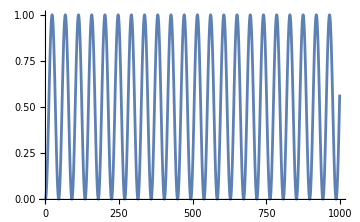

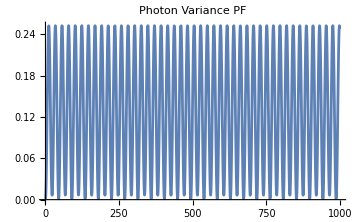

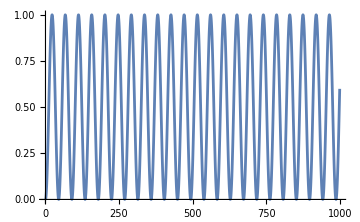

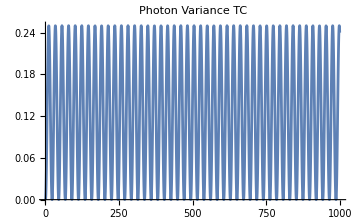

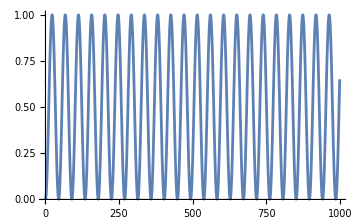

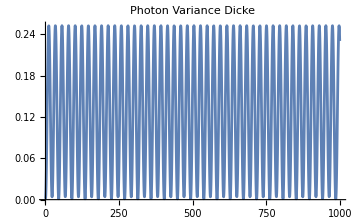

```mathematica
a=SparseArray[Band[{1,2}]->Table[Sqrt[n],{n,1,BSIZE-1}],{BSIZE,BSIZE}];
aDaggerA=KroneckerProduct[IdentityMatrix[NUMTLS+1],a†.a];
tMax =1000; 
h = 0.5;
tRange=Range[0,tMax,h];
ψs=Table[wfPF[time],{time,tRange}];
aDaggerAsr = aDaggerA.aDaggerA;
photons=Table[Conjugate[ψs[[n]]].aDaggerA.ψs[[n]],{n,Length@tRange}];
photonsvar = Table[Conjugate[ψs[[n]]].aDaggerAsr.ψs[[n]],{n,Length@tRange}]- photons^2;
ListLinePlot[{tRange,photons//Re}//Transpose,PlotRange->All,PlotLabel->"", ImageSize->Medium]
ListLinePlot[{tRange,photonsvar//Re}//Transpose,PlotRange->All,PlotLabel->"Photon Variance PF", ImageSize->Medium]
ψs=Table[wfTC[time],{time,tRange}];
photons=Table[Conjugate[ψs[[n]]].aDaggerA.ψs[[n]],{n,Length@tRange}];
photonsvar = Table[Conjugate[ψs[[n]]].aDaggerAsr.ψs[[n]],{n,Length@tRange}]- photons^2;
ListLinePlot[{tRange,photons//Re}//Transpose,PlotRange->All,PlotLabel->"", ImageSize->Medium]
ListLinePlot[{tRange,photonsvar//Re}//Transpose,PlotRange->All,PlotLabel->"Photon Variance TC", ImageSize->Medium]
ψs=Table[wfDicke[time],{time,tRange}];
photons=Table[Conjugate[ψs[[n]]].aDaggerA.ψs[[n]],{n,Length@tRange}];
photonsvar = Table[Conjugate[ψs[[n]]].aDaggerAsr.ψs[[n]],{n,Length@tRange}]- photons^2;
ListLinePlot[{tRange,photons//Re}//Transpose,PlotRange->All,PlotLabel->"", ImageSize->Medium]
ListLinePlot[{tRange,photonsvar//Re}//Transpose,PlotRange->All,PlotLabel->"Photon Variance Dicke", ImageSize->Medium]

(*Pauli Fierz*)
psiPF=Table[wfPF[time],{time,tRange}];
photonsPF=Table[Conjugate[psiPF[[n]]].aDaggerA.psiPF[[n]],{n,Length@tRange}];
plotPF=ListLinePlot[Transpose[{tRange,Re[photonsPF]}],PlotRange->All,PlotLabel->"",ImageSize->Medium];

(*Tavis-Cummings*)
psiTC=Table[wfTC[time],{time,tRange}];
photonsTC=Table[Conjugate[psiTC[[n]]].aDaggerA.psiTC[[n]],{n,Length@tRange}];
plotTC=ListLinePlot[Transpose[{tRange,Re[photonsTC]}],PlotRange->All,PlotLabel->"",ImageSize->Medium];

(*Dicke Model*)
psiD=Table[wfDicke[time],{time,tRange}];
photonsD=Table[Conjugate[psiD[[n]]].aDaggerA.psiD[[n]],{n,Length@tRange}];
plotD=ListLinePlot[Transpose[{tRange,Re[photonsD]}],PlotRange->All,PlotLabel->"",ImageSize->Medium];
(*plotPFmod=plotPF;
plotTCmod=Show[plotTC,AxesOrigin->Automatic,Ticks->{Automatic,None}];
plotDmod=Show[plotD,AxesOrigin->Automatic,Ticks->{Automatic,None}];*)

(*GraphicsRow[{plotPFmod,plotTCmod,plotDmod},Spacings->1,ImageSize->Full]*)
```

### Excitation Spectrum

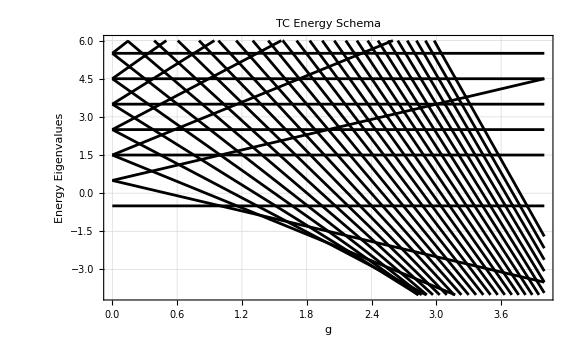

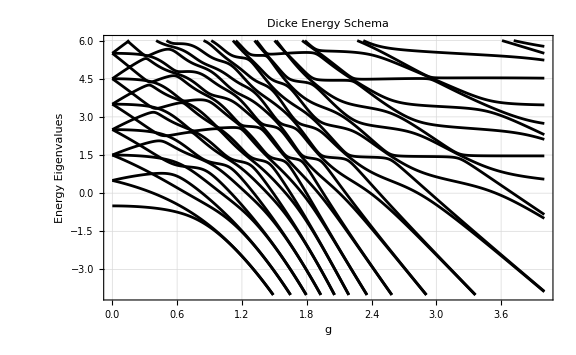

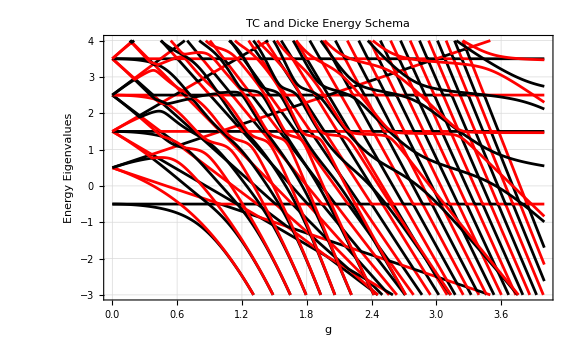

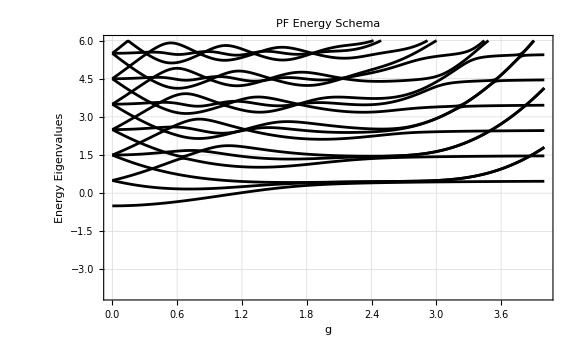

```mathematica
(*Define the range of coupling strengths*)
coupvals=Range[0,4.0,0.01];
(*Define the number of eigenvalues to plot*)
n=50;
(*Calculate eigenvalues for each coupling strength*)
eigv=Table[Sort[Eigenvalues[N[TCH[j]]]],{j,coupvals}];
(*Extract the first n eigenvalues*)
selectedeigv=Table[eigv[[All,i]],{i,n}];
(*Create the data for plotting*)
plot=Table[Thread[{coupvals,selectedeigv[[i]]}],{i,n}];
plotTC=Table[Thread[{coupvals,selectedeigv[[i]]}],{i,n}];
(*Plot the first n eigenvalues*)
ListLinePlot[plot,PlotRange->{{0,4.0},{-4.0,6}},PlotTheme->"Detailed",ImageSize->Large,PlotStyle->Directive[Black],PlotLabel->"TC Energy Schema",Frame->True,FrameLabel->{"g","Energy Eigenvalues"}]

eigv=Table[Sort[Eigenvalues[N[DH[j]]]],{j,coupvals}];
(*Extract the first n eigenvalues*)
selectedeigv=Table[eigv[[All,i]],{i,n}];
(*Create the data for plotting*)
plot=Table[Thread[{coupvals,selectedeigv[[i]]}],{i,n}];
plotDicke=Table[Thread[{coupvals,selectedeigv[[i]]}],{i,n}];
(*Plot the first n eigenvalues*)
ListLinePlot[plot,PlotRange->{{0,4.0},{-4.0,6}},PlotTheme->"Detailed",ImageSize->Large,PlotStyle->Directive[Black],PlotLabel->"Dicke Energy Schema",Frame->True,FrameLabel->{"g","Energy Eigenvalues"}]


(*Plot both schemas together*)
ListLinePlot[Join[plotTC,plotDicke],PlotRange->{{0,4.0},{-3.0,4}},PlotTheme->"Detailed",ImageSize->Large,PlotStyle->{Black,Red},PlotLabel->"TC and Dicke Energy Schema",Frame->True,FrameLabel->{"g","Energy Eigenvalues"}]


eigv=Table[Sort[Eigenvalues[N[PFH[j]]]],{j,coupvals}];
(*Extract the first n eigenvalues*)
selectedeigv=Table[eigv[[All,i]],{i,n}];
(*Create the data for plotting*)
plot=Table[Thread[{coupvals,selectedeigv[[i]]}],{i,n}];
(*Plot the first n eigenvalues*)
ListLinePlot[plot,
PlotRange->{{0,4},{-4.0, 6}},
PlotTheme->"Detailed", 
ImageSize->Large,
PlotStyle->Directive[Black], 
PlotLabel->"PF Energy Schema", Frame->True,FrameLabel->{"g","Energy Eigenvalues"}]
```